```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_CRIX/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | CRIX Price | log return future | log return CRIX
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 4387.15 | 0.0212907 | 0.0333146
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 4243.4 | -0.0904653 | -0.157294
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 4966.22 | -0.0196938 | -0.0120673
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 5026.51 | -0.131645 | -0.123533
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 5687.44 | 0.03685 | 0.0547603
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 5384.37 | -0.119603 | -0.109093
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 6005. | -0.042369 | -0.0285305
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 6178.8 | 0.018947 | 0.0208764
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 6051.14 | -0.0359909 | 0.003586)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return CRIX

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
α0=1.131743160;
β0=.0734943;
```

```mathematica
{α0,β0}
```

{0.861022,0.0407376}

```mathematica
For[kk=0, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
Print["Calibration..."];
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

0

Calibration...

```mathematica
{α0,β0}
```

{0.888306,0.0411777}

```mathematica
For[kk=0, kk≤ 0, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.989497694257557}. NIntegrate obtained 0.0718737 and 0.000112763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-13 | 0.932933 | 0.772844 | 0.834735 | 0.685776 | 0.769369 | 0.771882
 | 2021-05-06 | 0.93292 | 0.766897 | 0.793926 | 0.702302 | 0.755377 | 0.760124
 | 2021-04-29 | 0.934719 | 0.771552 | 0.797881 | 0.707181 | 0.759806 | 0.764469
 | 2021-04-22 | 0.93388 | 0.787482 | 0.850966 | 0.681158 | 0.775441 | 0.795129
 | 2021-04-15 | 0.935507 | 0.78363 | 0.82009 | 0.700605 | 0.768465 | 0.786609
 | 2021-04-08 | 0.936268 | 0.782892 | 0.81925 | 0.701505 | 0.767688 | 0.78799
 | 2021-04-01 | 0.937798 | 0.792251 | 0.824931 | 0.703216 | 0.773338 | 0.794772
 | 2021-03-25 | 0.939077 | 0.794834 | 0.824298 | 0.710088 | 0.775545 | 0.791333
 | 2021-03-18 | 0.938845 | 0.796252 | 0.822924 | 0.712111 | 0.775324 | 0.789989
 | 2021-03-11 | 0.939043 | 0.791524 | 0.812415 | 0.720572 | 0.77357 | 0.784521
 | 2021-03-04 | 0.939254 | 0.79361 | 0.82561 | 0.707562 | 0.773591 | 0.793916
 | 2021-02-25 | 0.937831 | 0.792482 | 0.826145 | 0.704109 | 0.772946 | 0.793658
 | 2021-02-18 | 0.937816 | 0.795484 | 0.828522 | 0.709503 | 0.768102 | 0.795014
 | 2021-02-10 | 0.941141 | 0.801155 | 0.831148 | 0.717876 | 0.77423 | 0.794424
 | 2021-01-28 | 0.942126 | 0.80763 | 0.845651 | 0.724025 | 0.78276 | 0.79689
 | 2021-01-21 | 0.944451 | 0.813679 | 0.846715 | 0.729715 | 0.789086 | 0.8033
 | 2021-01-13 | 0.940078 | 0.809298 | 0.836397 | 0.730467 | 0.775575 | 0.79906
 | 2021-01-06 | 0.942601 | 0.811688 | 0.865635 | 0.717473 | 0.785891 | 0.82958
 | 2020-12-29 | 0.941599 | 0.797648 | 0.846775 | 0.723585 | 0.77215 | 0.814195
 | 2020-12-21 | 0.942806 | 0.799829 | 0.850442 | 0.731919 | 0.780362 | 0.81174
 | 2020-12-14 | 0.938237 | 0.781594 | 0.816885 | 0.733108 | 0.758516 | 0.784655
 | 2020-12-07 | 0.941541 | 0.801074 | 0.850442 | 0.732446 | 0.780736 | 0.806214
 | 2020-11-27 | 0.934736 | 0.811779 | 0.803891 | 0.734 | 0.763443 | 0.766147
 | 2020-11-19 | 0.9489 | 0.839655 | 0.845614 | 0.768433 | 0.79566 | 0.805541
 | 2020-11-12 | 0.946461 | 0.838749 | 0.835535 | 0.760735 | 0.78851 | 0.798211
 | 2020-11-05 | 0.949698 | 0.848127 | 0.845435 | 0.766224 | 0.794962 | 0.818027
 | 2020-10-29 | 0.948319 | 0.845153 | 0.832834 | 0.764445 | 0.788976 | 0.809699
 | 2020-10-22 | 0.946303 | 0.831648 | 0.816731 | 0.764097 | 0.778425 | 0.79655
 | 2020-10-15 | 0.948417 | 0.842883 | 0.835126 | 0.763967 | 0.791301 | 0.799384
 | 2020-10-08 | 0.942224 | 0.825976 | 0.806456 | 0.749397 | 0.768504 | 0.78751
 | 2020-10-01 | 0.941231 | 0.824199 | 0.802409 | 0.746782 | 0.766001 | 0.784821
 | 2020-09-24 | 0.942777 | 0.825083 | 0.804538 | 0.748974 | 0.76779 | 0.790267
 | 2020-09-17 | 0.944379 | 0.825467 | 0.820271 | 0.746421 | 0.779302 | 0.792414
 | 2020-09-10 | 0.947088 | 0.827036 | 0.818613 | 0.748331 | 0.781392 | 0.798883
 | 2020-09-02 | 0.948608 | 0.817353 | 0.806789 | 0.754526 | 0.793545 | 0.80254
 | 2020-08-26 | 0.949058 | 0.817113 | 0.803601 | 0.753592 | 0.792168 | 0.806438
 | 2020-08-19 | 0.949688 | 0.812468 | 0.797963 | 0.75472 | 0.79009 | 0.808902
 | 2020-08-12 | 0.94859 | 0.804075 | 0.795344 | 0.751402 | 0.785918 | 0.806952
 | 2020-08-05 | 0.94868 | 0.829714 | 0.848812 | 0.741298 | 0.809934 | 0.829576
 | 2020-07-29 | 0.951732 | 0.813599 | 0.811342 | 0.756734 | 0.799901 | 0.816234
 | 2020-07-22 | 0.953077 | 0.836043 | 0.865196 | 0.749968 | 0.81816 | 0.832576
 | 2020-07-14 | 0.948073 | 0.819267 | 0.851376 | 0.731998 | 0.801534 | 0.829885
 | 2020-07-07 | 0.945339 | 0.809039 | 0.841185 | 0.725059 | 0.793561 | 0.822851
 | 2020-06-29 | 0.942268 | 0.787573 | 0.80975 | 0.726612 | 0.777238 | 0.797217
 | 2020-06-22 | 0.940514 | 0.778317 | 0.797553 | 0.723663 | 0.769416 | 0.790194
 | 2020-06-15 | 0.940204 | 0.773412 | 0.789297 | 0.722324 | 0.765401 | 0.789902
 | 2020-06-08 | 0.940741 | 0.764708 | 0.800708 | 0.727907 | 0.761159 | 0.789684
 | 2020-06-01 | 0.940673 | 0.764102 | 0.800403 | 0.7272 | 0.760661 | 0.78905
 | 2020-05-22 | 0.938617 | 0.760704 | 0.79865 | 0.723854 | 0.757769 | 0.784974
 | 2020-05-15 | 0.935479 | 0.755383 | 0.79128 | 0.716954 | 0.751011 | 0.778943
 | 2020-05-08 | 0.93274 | 0.751562 | 0.775463 | 0.714109 | 0.744515 | 0.776266
 | 2020-05-01 | 0.932826 | 0.751098 | 0.771221 | 0.715179 | 0.742509 | 0.773497
 | 2020-04-24 | 0.934807 | 0.753701 | 0.779826 | 0.718463 | 0.747799 | 0.775188
 | 2020-04-17 | 0.932858 | 0.753892 | 0.780347 | 0.713486 | 0.747176 | 0.773232
 | 2020-04-09 | 0.930382 | 0.749829 | 0.779277 | 0.708956 | 0.743685 | 0.771168
 | 2020-04-02 | 0.933415 | 0.760676 | 0.786537 | 0.712924 | 0.750454 | 0.779068
 | 2020-03-26 | 0.929259 | 0.749556 | 0.779588 | 0.706432 | 0.743486 | 0.770449
 | 2020-03-19 | 0.930084 | 0.76192 | 0.802995 | 0.700414 | 0.752681 | 0.77574
 | 2020-03-12 | 0.921223 | 0.758767 | 0.759754 | 0.686699 | 0.740353 | 0.765115
 | 2020-03-05 | 0.92314 | 0.752633 | 0.743484 | 0.676554 | 0.70561 | 0.763878
 | 2020-02-27 | 0.922166 | 0.75351 | 0.732487 | 0.688143 | 0.706371 | 0.756196
 | 2020-02-20 | 0.918913 | 0.741996 | 0.732521 | 0.668814 | 0.695786 | 0.755968
 | 2020-02-12 | 0.918226 | 0.743729 | 0.743523 | 0.673763 | 0.697777 | 0.752045
 | 2020-02-05 | 0.907325 | 0.720716 | 0.710059 | 0.658528 | 0.673819 | 0.73648
 | 2020-01-29 | 0.915277 | 0.731054 | 0.765231 | 0.651721 | 0.699452 | 0.74382
 | 2020-01-22 | 0.909595 | 0.719753 | 0.75752 | 0.631794 | 0.697461 | 0.731376
 | 2020-01-14 | 0.904832 | 0.716643 | 0.756062 | 0.617657 | 0.690438 | 0.725793
 | 2020-01-07 | 0.903021 | 0.714926 | 0.764891 | 0.610798 | 0.689367 | 0.72722
 | 2019-12-30 | 0.895929 | 0.71226 | 0.771962 | 0.604615 | 0.689669 | 0.714398
 | 2019-12-20 | 0.88917 | 0.694117 | 0.752332 | 0.588484 | 0.670446 | 0.70453
 | 2019-12-13 | 0.88598 | 0.690579 | 0.752655 | 0.580733 | 0.667561 | 0.701033
 | 2019-12-06 | 0.886089 | 0.690232 | 0.752681 | 0.580788 | 0.66757 | 0.701414
 | 2019-11-29 | 0.88544 | 0.693575 | 0.762108 | 0.573022 | 0.670148 | 0.707163
 | 2019-11-21 | 0.87925 | 0.68562 | 0.731772 | 0.580114 | 0.656849 | 0.679904
 | 2019-11-14 | 0.87475 | 0.67753 | 0.724624 | 0.577003 | 0.650605 | 0.673464
 | 2019-11-07 | 0.879044 | 0.681785 | 0.730842 | 0.577639 | 0.652748 | 0.680804
 | 2019-10-31 | 0.880723 | 0.678044 | 0.72636 | 0.581042 | 0.652559 | 0.68324
 | 2019-10-24 | 0.877737 | 0.681633 | 0.753626 | 0.568293 | 0.659932 | 0.686809
 | 2019-10-17 | 0.877589 | 0.682455 | 0.751003 | 0.566877 | 0.657349 | 0.688094
 | 2019-10-10 | 0.875674 | 0.674719 | 0.737935 | 0.564397 | 0.651717 | 0.679561
 | 2019-10-03 | 0.877602 | 0.675588 | 0.743493 | 0.56584 | 0.656211 | 0.682366
 | 2019-09-26 | 0.879855 | 0.678619 | 0.734795 | 0.571706 | 0.654485 | 0.685836
 | 2019-09-19 | 0.870142 | 0.664451 | 0.698766 | 0.577494 | 0.623496 | 0.672433
 | 2019-09-12 | 0.874267 | 0.673975 | 0.702685 | 0.589473 | 0.633963 | 0.674
 | 2019-09-05 | 0.87935 | 0.680799 | 0.698673 | 0.597424 | 0.636285 | 0.683171
 | 2019-08-28 | 0.878958 | 0.682752 | 0.723383 | 0.57958 | 0.639771 | 0.689248
 | 2019-08-21 | 0.876366 | 0.673577 | 0.7034 | 0.589317 | 0.632003 | 0.681325
 | 2021-05-20 | 0.931372 | 0.778548 | 0.838496 | 0.675028 | 0.774833 | 0.765473

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-13 | 0.841874 | 0.539044 | 0.555944 | 0.504936 | 0.55311 | 0.631953
 | 2021-05-06 | 0.905812 | 0.958385 | 0.939429 | 0.952741 | 0.941054 | -0.676412
 | 2021-04-29 | 0.850147 | 0.70833 | 0.596505 | 0.699581 | 0.604947 | 0.589857
 | 2021-04-22 | 0.949732 | 0.765716 | 0.835402 | 0.759537 | 0.829679 | 0.716464
 | 2021-04-15 | 0.946626 | 0.888496 | 0.960257 | 0.882778 | 0.957772 | 0.174227
 | 2021-04-08 | 0.94978 | 1.10624 | 0.907298 | 1.19111 | 0.926458 | 0.74228
 | 2021-04-01 | 0.96227 | 0.928904 | 0.979554 | 0.902713 | 0.977911 | 0.579868
 | 2021-03-25 | 0.949642 | -0.345621 | -0.363927 | -0.335711 | -0.363165 | 0.967641
 | 2021-03-18 | 0.981144 | 0.861526 | 0.865099 | 0.859017 | 0.864947 | 0.818339
 | 2021-03-11 | 0.899367 | 0.54789 | 0.578455 | 0.535186 | 0.576911 | 0.725533
 | 2021-03-04 | 0.771797 | 1.57778 | 1.68892 | 1.52489 | 1.6851 | 0.801507
 | 2021-02-25 | 0.956568 | 0.794107 | 0.837535 | 0.772582 | 0.836061 | 0.724242
 | 2021-02-18 | 0.992683 | 0.907609 | 0.92614 | 0.90356 | 0.93052 | 0.852779
 | 2021-02-10 | 0.838794 | 2.12753 | 2.37854 | 2.10452 | 2.29867 | 0.789823
 | 2021-01-28 | 0.846586 | 1.5949 | 1.8829 | 1.45904 | 1.86258 | 0.857939
 | 2021-01-21 | 0.920325 | 0.928507 | 0.8708 | 0.933741 | 0.873792 | 0.573608
 | 2021-01-13 | 0.960489 | 0.957462 | 0.934346 | 0.914569 | 0.938001 | 0.57711
 | 2021-01-06 | 0.982988 | 0.880617 | 0.880716 | 0.879858 | 0.881161 | 0.839274
 | 2020-12-29 | 0.777165 | 1.49512 | 1.81037 | 1.45369 | 1.8419 | 0.715859
 | 2020-12-21 | 0.978509 | 0.168595 | 0.17592 | 0.167946 | 0.177047 | 0.932438
 | 2020-12-14 | 0.997415 | 0.364696 | 0.339639 | 0.356055 | 0.378478 | 1.00533
 | 2020-12-07 | 0.985679 | 0.745696 | 0.705019 | 0.741002 | 0.673701 | 0.926978
 | 2020-11-27 | 0.995555 | 0.848245 | 0.694565 | 0.804094 | 0.734539 | 0.970154
 | 2020-11-19 | 0.842065 | 0.871045 | 0.873141 | 0.869079 | 0.874681 | -0.0365415
 | 2020-11-12 | 0.943431 | 0.270397 | 0.0832138 | 0.381546 | 0.0920753 | 0.869702
 | 2020-11-05 | 0.846895 | -0.546934 | -0.714404 | -0.500999 | -0.734315 | 0.712321
 | 2020-10-29 | 0.971529 | -39.3201 | -50.9474 | -43.4677 | -64.8027 | 0.944148
 | 2020-10-22 | 0.993227 | 0.809988 | 0.769798 | 0.776996 | 0.774942 | 1.05043
 | 2020-10-15 | 0.946035 | 0.468749 | 0.422682 | 0.457249 | 0.426699 | 0.893872
 | 2020-10-08 | 0.97177 | 0.767149 | 0.776142 | 0.770295 | 0.775637 | 0.868771
 | 2020-10-01 | 0.963897 | 0.669606 | 0.715368 | 0.687544 | 0.711074 | 0.89009
 | 2020-09-24 | 0.887294 | 0.749239 | 0.795779 | 0.763547 | 0.791228 | 0.631602
 | 2020-09-17 | 0.963301 | 0.745743 | 0.784933 | 0.752686 | 0.779114 | 0.848764
 | 2020-09-10 | 0.375517 | 2.62777 | 2.73611 | 2.66977 | 2.77693 | 0.579322
 | 2020-09-02 | 0.954486 | 0.712479 | 0.74169 | 0.7632 | 0.762584 | 0.801156
 | 2020-08-26 | 0.939214 | 0.824659 | 0.84815 | 0.8828 | 0.87804 | 0.55122
 | 2020-08-19 | 0.974832 | 0.905125 | 0.887425 | 0.904584 | 0.903609 | 0.759703
 | 2020-08-12 | 0.925444 | 0.733262 | 0.714795 | 0.742636 | 0.734429 | 0.663734
 | 2020-08-05 | 0.989577 | 0.867397 | 0.891665 | 0.865073 | 0.900074 | 0.914546
 | 2020-07-29 | 0.474372 | 0.627358 | 0.675365 | 0.627358 | 0.636593 | 0.100188
 | 2020-07-22 | 0.982413 | 2.08563 | 3.19864 | 1.18071 | 4.23108 | 0.883927
 | 2020-07-14 | 0.952613 | 0.567801 | 0.5831 | 0.565854 | 0.589364 | 0.839166
 | 2020-07-07 | 0.965559 | 0.924525 | 0.924525 | 0.924525 | 0.924525 | 0.752287
 | 2020-06-29 | 0.951706 | 0.772945 | 0.747193 | 0.742506 | 0.743904 | 0.796642
 | 2020-06-22 | 0.962045 | 0.820872 | 0.822261 | 0.826598 | 0.82565 | 0.724789
 | 2020-06-15 | 0.986545 | 0.938125 | 0.903982 | 0.938768 | 0.930689 | 0.861196
 | 2020-06-08 | 0.99519 | 0.947747 | 0.947348 | 0.947548 | 0.947298 | 0.909002
 | 2020-06-01 | 0.986763 | 0.562153 | 0.614341 | 0.587987 | 0.62176 | 0.939868
 | 2020-05-22 | 0.998735 | 0.915162 | 0.929244 | 0.924454 | 0.932056 | 0.97706
 | 2020-05-15 | 0.978139 | 0.969509 | 0.969752 | 0.968162 | 0.961684 | 0.800537
 | 2020-05-08 | 0.997678 | 0.895505 | 0.973633 | 0.971654 | 0.96699 | 0.983485
 | 2020-05-01 | 0.94459 | 2.6383 | 2.47178 | 2.434 | 2.40014 | 0.91792
 | 2020-04-24 | 0.979807 | 3.85818 | 3.75493 | 3.76679 | 3.74007 | 0.900812
 | 2020-04-17 | 0.990232 | 0.849906 | 0.886752 | 0.885955 | 0.889243 | 0.913825
 | 2020-04-09 | 0.992717 | 0.950363 | 0.950322 | 0.946791 | 0.947213 | 0.905994
 | 2020-04-02 | 0.978735 | 0.680769 | 0.672268 | 0.67147 | 0.671302 | 0.863102
 | 2020-03-26 | 0.993935 | 0.799198 | 0.797454 | 0.805923 | 0.804912 | 0.947698
 | 2020-03-19 | 0.990672 | 0.732836 | 0.771708 | 0.764006 | 0.762732 | 0.929145
 | 2020-03-12 | 0.993137 | 0.825024 | 0.873302 | 0.856751 | 0.875316 | 0.93999
 | 2020-03-05 | 0.991519 | 0.795756 | 0.935059 | 0.892236 | 0.898506 | 0.774928
 | 2020-02-27 | 0.941193 | 0.500954 | 0.503079 | 0.5125 | 0.497115 | 0.930903
 | 2020-02-20 | 0.967754 | 0.864525 | 0.880832 | 0.833504 | 0.833787 | 0.591174
 | 2020-02-12 | 0.952497 | 0.896748 | 0.909206 | 0.908723 | 0.902782 | 0.505009
 | 2020-02-05 | 0.858648 | 0.978166 | 1.67056 | 1.29569 | 1.64282 | 0.645551
 | 2020-01-29 | 0.937367 | 0.654224 | 0.688395 | 0.619479 | 0.659307 | 0.768496
 | 2020-01-22 | 0.989405 | 0.779346 | 0.898442 | 0.815658 | 0.859615 | 0.956697
 | 2020-01-14 | 0.985397 | 0.953634 | 1.00113 | 0.962736 | 0.982997 | 0.76572
 | 2020-01-07 | 0.969991 | 0.825671 | 0.918337 | 0.80316 | 0.877737 | 0.806332
 | 2019-12-30 | 0.928676 | 0.720397 | 0.418615 | 0.705375 | 0.593397 | 0.79423
 | 2019-12-20 | 0.903882 | 0.750221 | 0.742351 | 0.753574 | 0.746238 | 0.646931
 | 2019-12-13 | 0.9814 | 0.774288 | 0.817556 | 0.682912 | 0.772376 | 0.970814
 | 2019-12-06 | 0.965999 | 0.913657 | 0.883068 | 0.863832 | 0.926373 | 0.547666
 | 2019-11-29 | 0.996031 | 0.9461 | 0.944899 | 0.816538 | 0.970485 | 0.847764
 | 2019-11-21 | 0.990012 | 0.763052 | 0.802256 | 0.728169 | 0.798739 | 0.974976
 | 2019-11-14 | 0.989233 | 0.838701 | 0.96749 | 0.846867 | 0.914681 | 1.89435
 | 2019-11-07 | 0.972631 | 0.946155 | 0.924246 | 0.920293 | 0.938422 | 0.0633898
 | 2019-10-31 | 0.959115 | 0.823426 | 0.8233 | 0.895025 | 0.951605 | 0.72492
 | 2019-10-24 | 0.984237 | 0.0413024 | -0.472952 | 0.688659 | -0.13482 | 0.924136
 | 2019-10-17 | 0.99393 | 0.941193 | 0.941415 | 0.827022 | 0.953792 | 0.800232
 | 2019-10-10 | 0.973951 | 0.85962 | 0.944788 | 0.767231 | 0.902832 | 0.618368
 | 2019-10-03 | 0.982494 | 0.577287 | 0.531928 | 0.789517 | 0.83652 | 0.875268
 | 2019-09-26 | 0.96293 | 0.777206 | 0.776798 | 0.731495 | 0.778617 | 0.829935
 | 2019-09-19 | 0.998053 | 0.952081 | 0.952722 | 0.870751 | 0.940639 | 0.782562
 | 2019-09-12 | 0.847521 | 1.36155 | 1.34184 | 1.16591 | 1.25436 | 0.41558
 | 2019-09-05 | 0.837266 | 0.767465 | 0.799672 | 0.871456 | 0.85344 | 0.353553
 | 2019-08-28 | 0.98963 | 0.692917 | 0.249093 | 0.702763 | 0.631685 | 0.988033
 | 2019-08-21 | 0.981243 | 0.912826 | 0.901036 | 0.876933 | 0.913378 | 0.800609
 | 2021-05-20 | 0.958368 | 0.790257 | 0.801463 | 0.730426 | 0.795836 | 0.773359

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

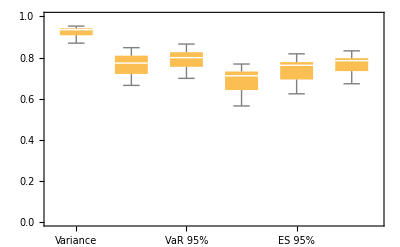

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

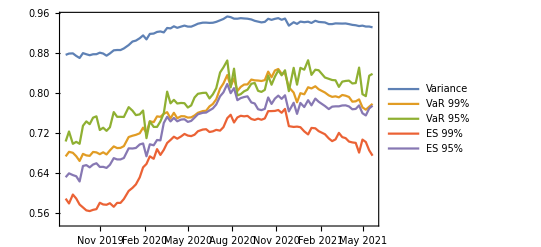

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

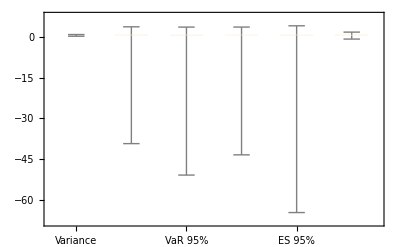

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

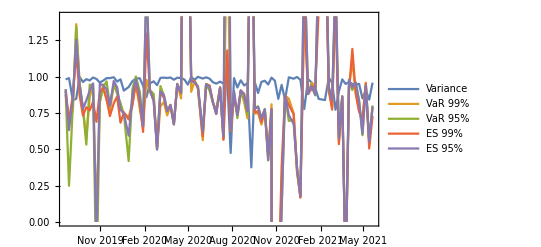

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return CRIX

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2021-05-20 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤1 (* 87 *), kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | CRIX Price | log return future | log return CRIX
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 5384.37 | -0.119603 | -0.109093
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 6005. | -0.042369 | -0.0285305
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 6178.8 | 0.018947 | 0.0208764
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 6051.14 | -0.0359909 | 0.003586
14 | 2021-05-07 20:00:00+00:00 | 57990. | BTCM1 Curncy | 6029.48 | 0.026384 | 0.0187656
15 | 2021-05-06 20:00:00+00:00 | 56480. | BTCM1 Curncy | 5917.39 | -0.0192019 | -0.00983699
16 | 2021-05-05 20:00:00+00:00 | 57575. | BTCM1 Curncy | 5975.89 | 0.0504024 | 0.0445594
17 | 2021-05-04 20:00:00+00:00 | 54745. | BTCM1 Curncy | 5715.45 | -0.0593936 | -0.0379611
18 | 2021-05-03 20:00:00+00:00 | 58095. | BTCM1 Curncy | 5936.59 | 0.00951235 | 0.0351896)

```mathematica
hvec
```

{{2021-05-13},{0.937278},{0.937245},{0.966629},{0.87794},{0.961702},{0.949392},{{0.03294108198418752, {h$181878731 -> 0.9372453194654965}},{0.01111115915148135, {h$181878731 -> 0.9666292047835696}},{0.06033748421402845, {h$181878731 -> 0.8779400114033828}},{0.026721210257471196, {h$181878731 -> 0.961702031999671}},{0.01638084400937566, {h$181878731 -> 0.9493921918965592}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤87, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤87, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk≤87, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤87, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

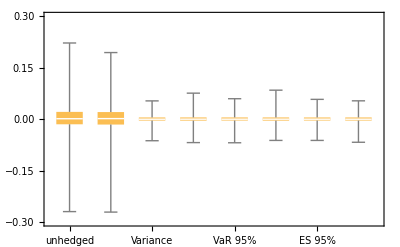

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

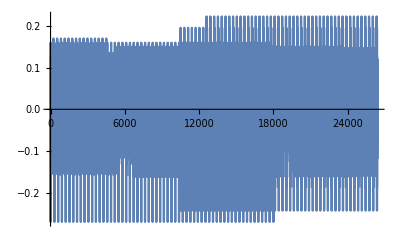

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤87, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

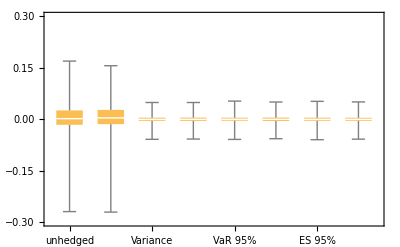

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

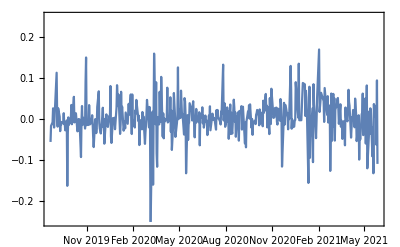
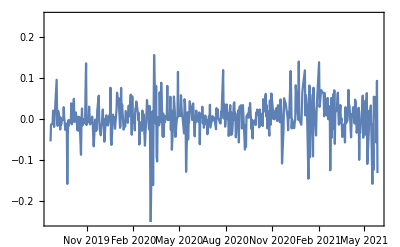

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

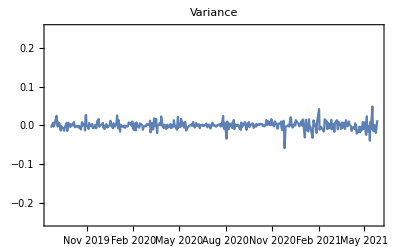
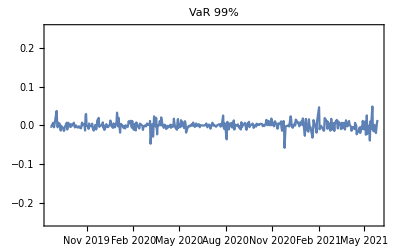
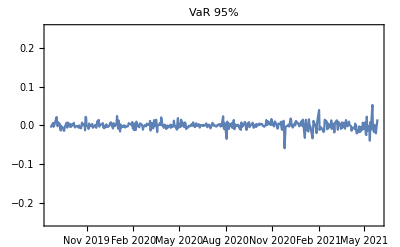
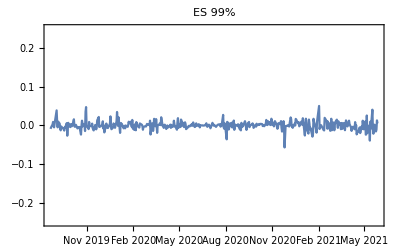
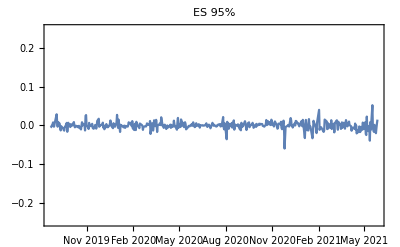
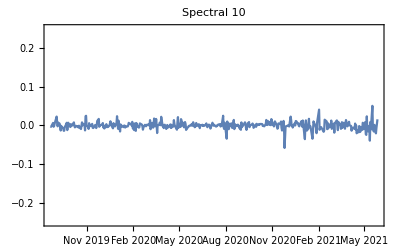

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤87, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

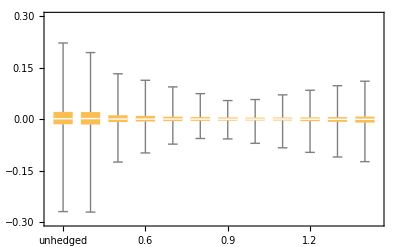

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤87, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

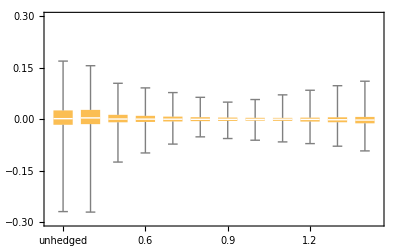

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤87, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.94872 | 0.95271 | 0.966219 | 0.880579 | 0.959436 | 0.966357
2021-05-13 | 0.937278 | 0.937245 | 0.966629 | 0.87794 | 0.961702 | 0.949392
2021-05-06 | 0.941392 | 0.883322 | 0.9617 | 0.906659 | 0.954979 | 0.946823
2021-04-29 | 0.945724 | 0.908388 | 0.960102 | 0.912434 | 0.956198 | 0.946083
2021-04-22 | 0.946059 | 0.891475 | 0.972606 | 0.884282 | 0.965943 | 0.975132
2021-04-15 | 0.947797 | 0.893474 | 0.965637 | 0.887724 | 0.963139 | 0.974812
2021-04-08 | 0.947859 | 0.924113 | 0.966134 | 0.88625 | 0.962087 | 0.962401
2021-04-01 | 0.94881 | 0.915555 | 0.965477 | 0.889741 | 0.963857 | 0.979435
2021-03-25 | 0.950812 | 0.917203 | 0.965783 | 0.890903 | 0.96376 | 0.979771
2021-03-18 | 0.948917 | 0.922853 | 0.96495 | 0.893301 | 0.963161 | 0.961209
2021-03-11 | 0.948914 | 0.911687 | 0.962548 | 0.890547 | 0.959978 | 0.981778
2021-03-04 | 0.949791 | 0.914612 | 0.964933 | 0.890662 | 0.963204 | 0.978674
2021-02-25 | 0.946562 | 0.915017 | 0.965057 | 0.890215 | 0.963359 | 0.973625
2021-02-18 | 0.946732 | 0.896215 | 0.973203 | 0.892216 | 0.964482 | 0.981624
2021-02-10 | 0.949196 | 0.904321 | 0.972513 | 0.895564 | 0.965052 | 0.970049
2021-01-28 | 0.953379 | 0.92157 | 0.97212 | 0.897724 | 0.968555 | 0.964214
2021-01-21 | 0.955155 | 0.90858 | 0.97255 | 0.902777 | 0.969233 | 0.982081
2021-01-13 | 0.953359 | 0.94341 | 0.971456 | 0.901145 | 0.967481 | 0.986509
2021-01-06 | 0.949746 | 0.943247 | 0.94769 | 0.90937 | 0.967524 | 1.00618
2020-12-29 | 0.94351 | 0.90937 | 0.951207 | 0.903872 | 0.955393 | 0.976341
2020-12-21 | 0.941879 | 0.910406 | 0.949964 | 0.906901 | 0.956047 | 0.967987
2020-12-14 | 0.940885 | 0.923016 | 0.9674 | 0.901145 | 0.962682 | 0.966166
2020-12-07 | 0.943829 | 0.913582 | 0.949964 | 0.907733 | 0.960141 | 0.959305
2020-11-27 | 0.942572 | 0.921801 | 0.968099 | 0.945481 | 0.959844 | 0.928814
2020-11-19 | 0.947308 | 0.931032 | 0.952822 | 0.910602 | 0.968831 | 0.936978
2020-11-12 | 0.94599 | 0.931794 | 0.968688 | 0.909886 | 0.966941 | 0.94507
2020-11-05 | 0.944678 | 0.924151 | 0.952801 | 0.916293 | 0.956208 | 0.948264
2020-10-29 | 0.945011 | 0.917472 | 0.938762 | 0.925067 | 0.964132 | 0.940545
2020-10-22 | 0.944145 | 0.914303 | 0.969213 | 0.959379 | 0.962185 | 0.942339
2020-10-15 | 0.943721 | 0.919902 | 0.969676 | 0.932328 | 0.965336 | 0.940148
2020-10-08 | 0.936707 | 0.904332 | 0.96172 | 0.92441 | 0.958499 | 0.943909
2020-10-01 | 0.934667 | 0.903215 | 0.964941 | 0.92741 | 0.959149 | 0.919856
2020-09-24 | 0.933596 | 0.903966 | 0.975467 | 0.921228 | 0.954625 | 0.943272
2020-09-17 | 0.934305 | 0.918435 | 0.9667 | 0.926986 | 0.959533 | 0.91806
2020-09-10 | 0.934394 | 0.905582 | 0.94292 | 0.920058 | 0.956985 | 0.928264
2020-09-02 | 0.923272 | 0.892356 | 0.928942 | 0.955883 | 0.955111 | 0.913763
2020-08-26 | 0.920152 | 0.892877 | 0.918312 | 0.955828 | 0.950674 | 0.913626
2020-08-19 | 0.919349 | 0.958922 | 0.913452 | 0.957462 | 0.954828 | 0.917338
2020-08-12 | 0.918092 | 0.948189 | 0.924308 | 0.960311 | 0.949698 | 0.917283
2020-08-05 | 0.918103 | 0.900406 | 0.927902 | 0.897772 | 0.943833 | 0.917898
2020-07-29 | 0.920955 | 0.959602 | 0.928987 | 0.959602 | 0.953713 | 0.915919
2020-07-22 | 0.924051 | 0.916075 | 0.932407 | 0.902796 | 0.947556 | 0.920622
2020-07-14 | 0.916927 | 0.8941 | 0.921184 | 0.890652 | 0.932275 | 0.92585
2020-07-07 | 0.915597 | 0.899188 | 0.92327 | 0.885474 | 0.929772 | 0.918384
2020-06-29 | 0.912646 | 0.89508 | 0.934458 | 0.941624 | 0.939488 | 0.905804
2020-06-22 | 0.911862 | 0.915805 | 0.923715 | 0.948421 | 0.943021 | 0.922834
2020-06-15 | 0.912667 | 0.953597 | 0.918891 | 0.95425 | 0.946037 | 0.903977
2020-06-08 | 0.91783 | 0.960763 | 0.945329 | 0.953053 | 0.943414 | 0.920625
2020-06-01 | 0.918046 | 0.960112 | 0.945236 | 0.952748 | 0.943122 | 0.913854
2020-05-22 | 0.917194 | 0.958239 | 0.944746 | 0.949336 | 0.942052 | 0.936634
2020-05-15 | 0.915465 | 0.948372 | 0.948609 | 0.947054 | 0.940717 | 0.922234
2020-05-08 | 0.914923 | 0.871292 | 0.949653 | 0.945382 | 0.940845 | 0.928668
2020-05-01 | 0.916199 | 0.970953 | 0.950306 | 0.94502 | 0.940282 | 0.926599
2020-04-24 | 0.921262 | 0.966729 | 0.945485 | 0.947924 | 0.942427 | 0.925674
2020-04-17 | 0.921412 | 0.852393 | 0.944479 | 0.94502 | 0.942788 | 0.91749
2020-04-09 | 0.919813 | 0.945562 | 0.945521 | 0.942007 | 0.942427 | 0.932624
2020-04-02 | 0.921807 | 0.958163 | 0.946197 | 0.945074 | 0.944838 | 0.930294
2020-03-26 | 0.920872 | 0.9448 | 0.945524 | 0.942007 | 0.942427 | 0.928612
2020-03-19 | 0.922522 | 0.857697 | 0.935756 | 0.944715 | 0.946197 | 0.914519
2020-03-12 | 0.916761 | 0.884207 | 0.943714 | 0.923314 | 0.946197 | 0.918525
2020-03-05 | 0.919884 | 0.800075 | 0.940134 | 0.897079 | 0.903383 | 0.95348
2020-02-27 | 0.925177 | 0.905179 | 0.909018 | 0.926041 | 0.898242 | 0.968754
2020-02-20 | 0.921503 | 0.928636 | 0.946152 | 0.895315 | 0.895618 | 0.954608
2020-02-12 | 0.921877 | 0.886119 | 0.942456 | 0.926926 | 0.901219 | 0.941838
2020-02-05 | 0.916957 | 0.917539 | 0.873585 | 0.901612 | 0.884201 | 0.954331
2020-01-29 | 0.912086 | 0.882841 | 0.928954 | 0.835955 | 0.889701 | 0.923742
2020-01-22 | 0.911114 | 0.815569 | 0.961511 | 0.853569 | 0.899569 | 0.943258
2020-01-14 | 0.909748 | 0.810433 | 0.944606 | 0.836145 | 0.893378 | 0.943426
2020-01-07 | 0.907793 | 0.827392 | 0.951884 | 0.797149 | 0.897341 | 0.919609
2019-12-30 | 0.905659 | 0.792769 | 0.927436 | 0.767163 | 0.882933 | 0.936366
2019-12-20 | 0.905129 | 0.825147 | 0.959455 | 0.767922 | 0.893118 | 0.926249
2019-12-13 | 0.904875 | 0.899421 | 0.964741 | 0.761476 | 0.896536 | 0.923127
2019-12-06 | 0.905144 | 0.91342 | 0.954048 | 0.762303 | 0.896531 | 0.923121
2019-11-29 | 0.910173 | 0.867559 | 0.949479 | 0.748753 | 0.899168 | 0.936392
2019-11-21 | 0.915764 | 0.860108 | 0.953478 | 0.820788 | 0.900333 | 0.907787
2019-11-14 | 0.915578 | 0.81568 | 0.962836 | 0.823622 | 0.889574 | 0.939338
2019-11-07 | 0.91985 | 0.849124 | 0.964042 | 0.824674 | 0.906688 | 0.933265
2019-10-31 | 0.921439 | 0.965616 | 0.965668 | 0.83828 | 0.913285 | 0.941094
2019-10-24 | 0.924663 | 0.907603 | 0.966585 | 0.781214 | 0.927803 | 0.94131
2019-10-17 | 0.931506 | 0.96855 | 0.967951 | 0.777476 | 0.934442 | 0.947622
2019-10-10 | 0.930332 | 0.884257 | 0.971867 | 0.78922 | 0.928708 | 0.941179
2019-10-03 | 0.931425 | 0.964333 | 0.969986 | 0.79078 | 0.932028 | 0.947995
2019-09-26 | 0.931784 | 0.963009 | 0.973546 | 0.811603 | 0.926542 | 0.941984
2019-09-19 | 0.92762 | 0.953212 | 0.987252 | 0.846098 | 0.914008 | 0.943324
2019-09-12 | 0.930418 | 0.973356 | 0.959263 | 0.833492 | 0.896725 | 0.964737
2019-09-05 | 0.937174 | 0.983312 | 0.95277 | 0.844778 | 0.901782 | 0.965647
2019-08-28 | 0.939944 | 0.811525 | 0.974358 | 0.797166 | 0.90082 | 0.961447
2019-08-21 | 0.941209 | 0.962106 | 0.98619 | 0.854192 | 0.916801 | 0.975961)

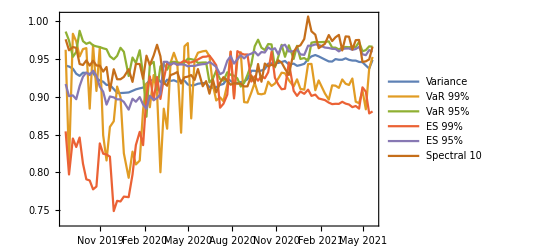

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```